```mathematica
(* If the second argument of α or M is 0 that means it's appropriate for a dimension with Dirichlet boundary conditions, if it's 1, then that means it's appropriate for a dimension with Neumann boundary conditions *)
```

```mathematica
(* The α are related to the positions of the grid points *)
```

```mathematica
α[i_,0]:=BesselJZero[0,i]
α[i_,1]:=BesselJZero[1,i-1]
α[1,1]:=0
```

```mathematica
(* The M are related to the quasi-Gaussian quadrature weight (the weight is just 'r dr' or 'k dk' appropriately discretised) *)
```

```mathematica
M[i_,0]:=BesselJ[1,α[i,0]]^2
M[i_,1]:=BesselJ[0,α[i,1]]^2
```

```mathematica
(* 
If id=0,1 then we're transforming *to* a dimension with Dirichlet, Neumann boundary conditions respectively
If jd=0,1 then we're transforming *from* a dimension with Dirichlet, Neumann boundary conditions respectively
*)
```

```mathematica
T[Nmax_,id_,jd_,S_]:=2/S Table[1/M[i,id] BesselJ[0,(α[i,id]α[j,jd])/S],{i,1,Nmax},{j,1,Nmax}]
```

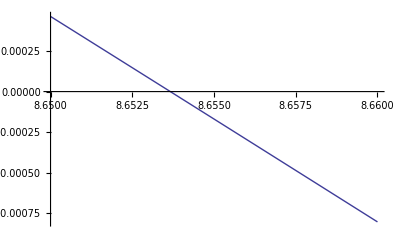

```mathematica
Plot[Evaluate[Abs[Det[T[2,0,0,S]]]-1],{S,8.65,8.66}]
```

```mathematica
N[α[3,0]]
```

8.65373

```mathematica
FrobeniusNorm[matrix_]:=√Total[matrix^2,∞]
```

```mathematica
Error[matrix_]:=matrix-IdentityMatrix[Length[matrix]]
```

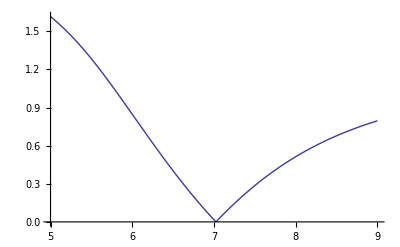

```mathematica
Plot[Evaluate[FrobeniusNorm[Error[T[2,0,1,S].T[2,1,0,S]]]],{S,5,9}]
```

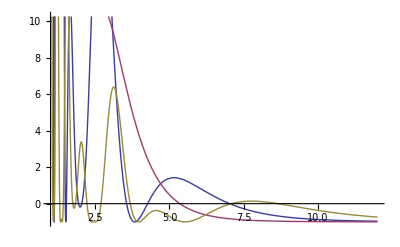

```mathematica
Plot[{Evaluate[Abs[Det[T[2,0,1,S].T[2,1,0,S]]]-1],Evaluate[Abs[Det[T[2,1,1,S].T[2,1,1,S]]]-1],Evaluate[Abs[Det[T[2,0,0,S].T[2,0,0,S]]]-1]},{S,1,12}]
```

```mathematica
FindMinValue[Evaluate[FrobeniusNorm[Error[T[2,0,1,S].T[2,1,0,S]]]],{S,1/2(α[2,0]+α[3,0])},WorkingPrecision->30]
```

0.00140916203393541654265958912482

```mathematica
FindMinValue[Evaluate[FrobeniusNorm[Error[T[2,1,1,S].T[2,1,1,S]]]],{S,1/2(α[2,1]+α[3,1])},WorkingPrecision->30]
```

0.00251801871557528571160930086789

```mathematica
FindMinValue[Evaluate[FrobeniusNorm[Error[T[2,0,0,S].T[2,0,0,S]]]],{S,α[3,0]},WorkingPrecision->30]
```

1.73123399465147524447134047676×10^-7

```mathematica
dd[Nmax_]:=FindMinValue[Evaluate[FrobeniusNorm[Error[T[Nmax,0,0,S].T[Nmax,0,0,S]]]],{S,α[Nmax+1,0]},WorkingPrecision->30]
```

```mathematica
dn[Nmax_]:=FindMinValue[Evaluate[FrobeniusNorm[Error[T[Nmax,0,1,S].T[Nmax,1,0,S]]]],{S,1/2(α[Nmax,0]+α[Nmax+1,0])},WorkingPrecision->30]
```

```mathematica
nn[Nmax_]:=FindMinValue[Evaluate[FrobeniusNorm[Error[T[Nmax,1,1,S].T[Nmax,1,1,S]]]],{S,1/2(α[Nmax,1]+α[Nmax+1,1])},WorkingPrecision->30]
```

```mathematica
{dd[5],dn[5],nn[5]}
```

{3.04604560471890748246855374884×10^-7,0.00121019891541586465059114072055,0.0023225644830393213118347075378}

```mathematica
Table[FindMinimum[Evaluate[FrobeniusNorm[Error[T[2,0,1,S].T[2,1,0,S]]]],{S,S0},WorkingPrecision->30],{S0,{3.5,4.5,7}}]
```

{{0.00140916203393541654265958912482,{S→7.02429341025245819361514816335}},{0.00140916203393541654265958912482,{S→-7.02429341025245819361514924442}},{0.00140916203393541654265958912482,{S→7.02429341025245819361514765345}}}

```mathematica
Table[FindMinimum[Evaluate[FrobeniusNorm[Error[T[2,0,0,S].T[2,0,0,S]]]],{S,S0},WorkingPrecision->30],{S0,{3.5,7,8.5}}]
```

{{2.01861240902364872941990815109,{S→3.3499272336689517871017486124}},{1.73123399465147524447134047676×10^-7,{S→8.65366486102125035353806802096}},{1.73123399465147524447134047676×10^-7,{S→8.65366486102125035353806801575}}}

```mathematica
Plot[{Evaluate@FrobeniusNorm[Error[T[2,0,1,S].T[2,1,0,S]]],Evaluate@FrobeniusNorm[Error[T[2,1,1,S].T[2,1,1,S]]],Evaluate@FrobeniusNorm[Error[T[2,0,0,S].T[2,0,0,S]]]},{S,4,9}]
```

$Aborted

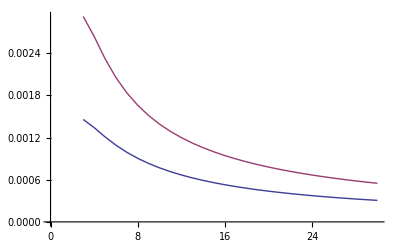

```mathematica
ListLinePlot[Table[Table[{Nmax,f[Nmax]},{Nmax,3,30}],{f,{dn,nn}}]]
```

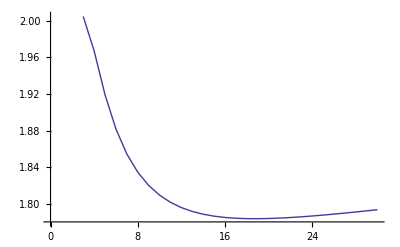

```mathematica
ListLinePlot[Table[{Nmax,nn[Nmax]/dn[Nmax]},{Nmax,3,30}]]
```

```mathematica
N[nn[50]/dn[50]]
```

1.81954

```mathematica
FindMinimum[Evaluate[FrobeniusNorm[Error[T[5,1,1,S].T[5,1,1,S]]]],{S,15},WorkingPrecision->30]
```

{0.0023225644830393213118347075378,{S→14.8668959607400875874055637748}}

```mathematica
FindRoot[Abs[Det[T[5,1,1,S]]]-1,{S,15},WorkingPrecision->30]
```

{S→14.8680449570494125700122934743}

```mathematica
N[T[5,1,1,14.8668959607400875874055637747886266670945196165641462421914`30.]-Inverse[T[5,1,1,14.8668959607400875874055637747886266670945196165641462421914`30.]]]//MatrixForm
```

(-0.000166501 | 0.0000698022 | -0.0000556464 | 0.0000398742 | 0.000125436
0.000430306 | -0.000180468 | 0.000144274 | -0.000106369 | -0.00028121
-0.000617816 | 0.000259837 | -0.000210231 | 0.000167404 | 0.000264639
0.000639496 | -0.000276727 | 0.000241819 | -0.000237332 | -0.0000361573
0.00263075 | -0.000956704 | 0.000499904 | -0.0000472831 | -0.000520458)

```mathematica
Det[T[5,1,1,14.8680449570494125700122934743017743657653536872661598412259`30.]]
```

1.

```mathematica
T[5,1,1,14.8680449570494125700122934743017743657653536872661598412259`30.].Inverse[T[5,1,1,14.8680449570494125700122934743017743657653536872661598412259`30.]]-IdentityMatrix[5]
```

{{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.}}